# Data for San Marco catchment

## Preliminaries

```mathematica
SetDirectory["C:\\Users\\ulzegasi\\Julia_files\\ParInf_HMC"]
Needs["CustomTicks`"]
```

C:\Users\ulzegasi\Julia_files\ParInf_HMC

## Data

```mathematica
sanmarco raw=Drop[Import["SanMarco.dat"],6];

(* Row 1 contains the headers for the columns*)
sanmarco raw[[1]]
sanmarco raw[[1,7]]
sanmarco raw[[1,8]]
sanmarco raw[[1,9]]
```

{Year,,Month,,Day,,Hour,,Min,,QC,,Disch,,Prec,,Etp,,Temp}

Disch,

Prec,

Etp,

```mathematica
(* We first look at the years 1996-1997 *)
y96=Flatten[Position[sanmarco raw[[All,1]],1996]];
y97=Flatten[Position[sanmarco raw[[All,1]],1997]];

disc=sanmarco raw[[Join[y96,y97],7]]; (* river discharge *)
prec=sanmarco raw[[Join[y96,y97],8]]; (* precipitation *)
evap=sanmarco raw[[Join[y96,y97],9]]; (* evaporation *)

(* How many days without rain (in 2 years)? *)
count=0;Do[If[prec[[i]]==0,count+=1],{i,1,Length[prec]}];count
count/Length[prec]*100.0 (*no rain %*)
```

252

34.4733

```mathematica
rain=prec-evap;  (* effective rain is precipitation - evaporation *)
```

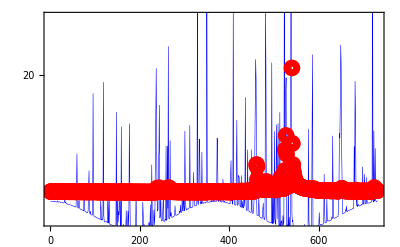

```mathematica
Show[
ListPlot[rain,Joined->True,AxesOrigin->{0,0},PlotStyle->Directive[Thickness[0.001],Blue],PlotRange->All],
ListPlot[disc,Joined->False,AxesOrigin->{0,0},PlotMarkers->Graphics[{Red,Thickness[5],Circle[]},ImageSize->10]],
Axes->True,Frame->True,FrameStyle->Directive[Thick,16,Bold],FrameTicks->{LinTicks[0,800,100,4,MajorTickLength->0.015,MajorTickStyle->{Thick},MinorTickLength->0.01,MinorTickStyle->{Thick}],LinTicks[-20,200,10,5,MajorTickLength->0.015,MajorTickStyle->{Thick},MinorTickLength->0.01,MinorTickStyle->{Thick}],None,None},PlotRange->{All,{-5,30}}]
```

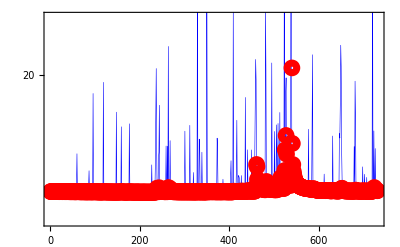

```mathematica
(* effective rain cannot be negative *)
Do[If[rain[[i]]<=0,rain[[i]]=0.001],{i,1,Length[prec]}];
Show[ListPlot[rain,Joined->True,AxesOrigin->{0,0},PlotStyle->Directive[Thickness[0.001],Blue],PlotRange->All],
ListPlot[disc,Joined->False,AxesOrigin->{0,0},PlotMarkers->Graphics[{Red,Thickness[5],Circle[]},ImageSize->10]],Axes->True,Frame->True,FrameStyle->Directive[Thick,16,Bold],FrameTicks->{LinTicks[0,800,100,4,MajorTickLength->0.015,MajorTickStyle->{Thick},MinorTickLength->0.01,MinorTickStyle->{Thick}],LinTicks[-20,200,10,5,MajorTickLength->0.015,MajorTickStyle->{Thick},MinorTickLength->0.01,MinorTickStyle->{Thick}],None,None},PlotRange->{All,{-5,30}}]
```

## Smoothing and interpolating the rain

12

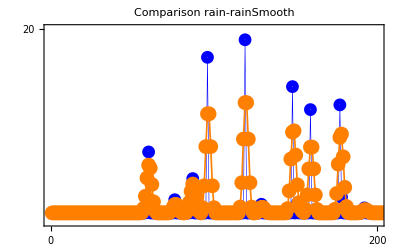

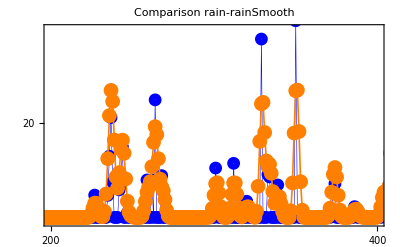

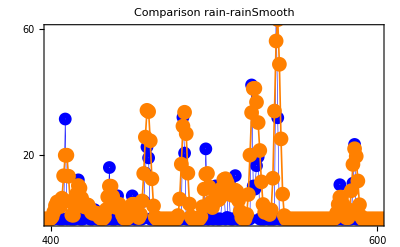

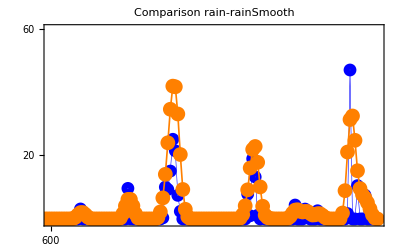

```mathematica
rainSmooth=3.0*LowpassFilter[rain,0.7];
counter=0;Do[If[rainSmooth[[i]]≤0,counter+=1],{i,1,Length[rainSmooth]}];counter (* check that smooth rain is non-zero*)
Show[
ListPlot[rain,Joined->True,AxesOrigin->{0,0},PlotMarkers->Graphics[{Blue,Thickness[5],Circle[]},ImageSize->6],PlotStyle->Directive[Thickness[0.001],Blue]],
ListPlot[rainSmooth,Joined->True,AxesOrigin->{0,0},PlotMarkers->Graphics[{Orange,Thickness[5],Circle[]},ImageSize->8],PlotStyle->Directive[Thickness[0.003],Orange]],
PlotRange->{{0,200},{-1,20}},
Axes->True,Frame->True,FrameStyle->Directive[Thick,16,Bold],FrameTicks->{LinTicks[0,800,100,4,MajorTickLength->0.015,MajorTickStyle->{Thick},MinorTickLength->0.01,MinorTickStyle->{Thick}],LinTicks[-20,200,10,5,MajorTickLength->0.015,MajorTickStyle->{Thick},MinorTickLength->0.01,MinorTickStyle->{Thick}],None,None},PlotLabel->"Comparison rain-rainSmooth"
]
Show[
ListPlot[rain,Joined->True,AxesOrigin->{0,0},PlotMarkers->Graphics[{Blue,Thickness[5],Circle[]},ImageSize->6],PlotStyle->Directive[Thickness[0.001],Blue]],
ListPlot[rainSmooth,Joined->True,AxesOrigin->{0,0},PlotMarkers->Graphics[{Orange,Thickness[5],Circle[]},ImageSize->8],PlotStyle->Directive[Thickness[0.003],Orange],PlotRange->All],
PlotRange->{{200,400},{-1,40}},
Axes->True,Frame->True,FrameStyle->Directive[Thick,16,Bold],FrameTicks->{LinTicks[0,800,100,4,MajorTickLength->0.015,MajorTickStyle->{Thick},MinorTickLength->0.01,MinorTickStyle->{Thick}],LinTicks[-20,200,10,5,MajorTickLength->0.015,MajorTickStyle->{Thick},MinorTickLength->0.01,MinorTickStyle->{Thick}],None,None},PlotLabel->"Comparison rain-rainSmooth"
]
Show[
ListPlot[rain,Joined->True,AxesOrigin->{0,0},PlotMarkers->Graphics[{Blue,Thickness[5],Circle[]},ImageSize->6],PlotStyle->Directive[Thickness[0.001],Blue]],
ListPlot[rainSmooth,Joined->True,AxesOrigin->{0,0},PlotMarkers->Graphics[{Orange,Thickness[5],Circle[]},ImageSize->8],PlotStyle->Directive[Thickness[0.003],Orange],PlotRange->All],
PlotRange->{{400,600},{-1,60}},
Axes->True,Frame->True,FrameStyle->Directive[Thick,16,Bold],FrameTicks->{LinTicks[0,800,100,4,MajorTickLength->0.015,MajorTickStyle->{Thick},MinorTickLength->0.01,MinorTickStyle->{Thick}],LinTicks[-20,200,10,5,MajorTickLength->0.015,MajorTickStyle->{Thick},MinorTickLength->0.01,MinorTickStyle->{Thick}],None,None},PlotLabel->"Comparison rain-rainSmooth"
]
Show[
ListPlot[rain,Joined->True,AxesOrigin->{0,0},PlotMarkers->Graphics[{Blue,Thickness[5],Circle[]},ImageSize->6],PlotStyle->Directive[Thickness[0.001],Blue]],
ListPlot[rainSmooth,Joined->True,AxesOrigin->{0,0},PlotMarkers->Graphics[{Orange,Thickness[5],Circle[]},ImageSize->8],PlotStyle->Directive[Thickness[0.003],Orange],PlotRange->All],
PlotRange->{{600,731},{-1,60}},
Axes->True,Frame->True,FrameStyle->Directive[Thick,16,Bold],FrameTicks->{LinTicks[0,800,100,4,MajorTickLength->0.015,MajorTickStyle->{Thick},MinorTickLength->0.01,MinorTickStyle->{Thick}],LinTicks[-20,200,10,5,MajorTickLength->0.015,MajorTickStyle->{Thick},MinorTickLength->0.01,MinorTickStyle->{Thick}],None,None},PlotLabel->"Comparison rain-rainSmooth"
]
```

```mathematica
Length[rain]
Length[rainSmooth]
```

731

731

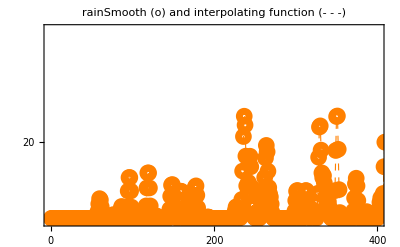

```mathematica
(* Generate interpolating function *) rainInt=Interpolation[rainSmooth,InterpolationOrder->5];

Show[Plot[rainInt[x],{x,1,731},PlotStyle->{Dashed,Orange,Thickness[0.002]},PlotRange->All],
ListPlot[rainSmooth,Joined->False,AxesOrigin->{0,0},PlotMarkers->Graphics[{Orange,Thickness[5],Circle[]},ImageSize->10],PlotStyle->Directive[Thickness[0.003],Orange]],
PlotRange->{{0,400},{-1,50}},
Axes->True,Frame->True,FrameStyle->Directive[Thick,16,Bold],FrameTicks->{LinTicks[0,800,100,4,MajorTickLength->0.015,MajorTickStyle->{Thick},MinorTickLength->0.01,MinorTickStyle->{Thick}],LinTicks[-20,200,10,5,MajorTickLength->0.015,MajorTickStyle->{Thick},MinorTickLength->0.01,MinorTickStyle->{Thick}],None,None},PlotLabel->Style["rainSmooth (o) and interpolating function (- - -)",16,Blue]
]
```

## Generate “extended” rain data with staging points

```mathematica
rainExt=Table[{x,rainInt[x]},{x,1,731,0.1}];
(* Here we have implicitly assumed n = 730, j = 10, therefore we will have N = n*j +1 = 7301 *)
(* The number of data points (= boundary beads) is n+1 = 731, while the number of staging points in each segment is j-1 = 9 *)
Length[rainExt] (* should be N = 7301 *)
```

7301

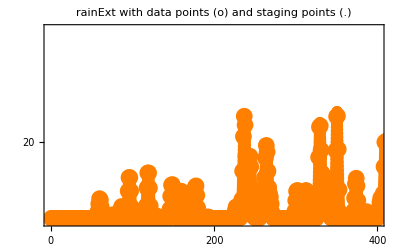

```mathematica
Show[
ListPlot[rainSmooth,Joined->False,AxesOrigin->{0,0},PlotMarkers->Graphics[{Orange,Thickness[5],Circle[]},ImageSize->10],PlotStyle->Directive[Thickness[0.003],Orange]],
ListPlot[rainExt,Joined->False,AxesOrigin->{0,0},PlotMarkers->Graphics[{Orange,Thickness[5],Circle[]},ImageSize->4],PlotStyle->Directive[Thickness[0.003],Orange]],
PlotRange->{{0,400},{-1,50}},
Axes->True,Frame->True,FrameStyle->Directive[Thick,16,Bold],FrameTicks->{LinTicks[0,800,100,4,MajorTickLength->0.015,MajorTickStyle->{Thick},MinorTickLength->0.01,MinorTickStyle->{Thick}],LinTicks[-20,200,10,5,MajorTickLength->0.015,MajorTickStyle->{Thick},MinorTickLength->0.01,MinorTickStyle->{Thick}],None,None},PlotLabel->Style["rainExt with data points (o) and staging points (.)",16,Blue]
]
```

```mathematica
counter=0;Do[If[rainExt[[i,2]]≤0,counter+=1],{i,1,Length[rainExt]}];counter (* check that rain is non-zero*)
If[counter>0,
rainExtOld=rainExt;
rainExt[[All,2]]+=Abs[Min[rainExt[[All,2]]]]+0.001];
counter=0;Do[If[rainExt[[i,2]]≤0,counter+=1],{i,1,Length[rainExt]}];counter (* check again that rain is non-zero*)
```

295

0

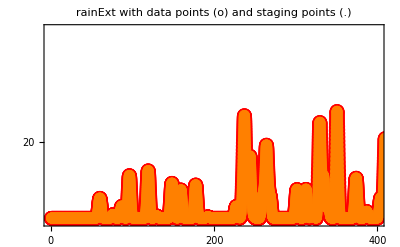

```mathematica
Show[
ListPlot[rainExtOld,Joined->False,AxesOrigin->{0,0},PlotMarkers->Graphics[{Red,Thickness[5],Circle[]},ImageSize->8],PlotStyle->Directive[Thickness[0.003],Red]],
ListPlot[rainExt,Joined->False,AxesOrigin->{0,0},PlotMarkers->Graphics[{Orange,Thickness[5],Circle[]},ImageSize->4],PlotStyle->Directive[Thickness[0.003],Orange]],
PlotRange->{{0,400},{-1,50}},
Axes->True,Frame->True,FrameStyle->Directive[Thick,16,Bold],FrameTicks->{LinTicks[0,800,100,4,MajorTickLength->0.015,MajorTickStyle->{Thick},MinorTickLength->0.01,MinorTickStyle->{Thick}],LinTicks[-20,200,10,5,MajorTickLength->0.015,MajorTickStyle->{Thick},MinorTickLength->0.01,MinorTickStyle->{Thick}],None,None},PlotLabel->Style["rainExt with data points (o) and staging points (.)",16,Blue]
]
```

## Export data

```mathematica
Export["rain.dat",rainExt]
Export["disc.dat",disc]
```

rain.dat

disc.dat